# Revisiting coin projections

## Definitions

## DTQW Environment

```mathematica
$DTQWEnvIcon=Graphics[{
Thick,
Circle[],
PointSize[Large],
Point[{0,0}]
},
ImageSize->Dynamic[{
Automatic,
3.5 CurrentValue["FontCapHeight"]/AbsoluteCurrentValue[Magnification]
}]
];
```

```mathematica
DTQWEnvAscQ[asc_?AssociationQ]:=And[
AllTrue[{"Type","Decoherent"},KeyExistsQ[asc,#]&],
Or[KeyExistsQ[asc,"Unitary"],AllTrue[{"Shift","Coin"},KeyExistsQ[asc,#]&]],
Xnor[asc["Decoherent"],AllTrue[{"Kraus","Probabilities"},KeyExistsQ[asc,#]&]],
Xnor[asc["Type"]=="FixedSize",KeyExistsQ[asc,"Size"]]
]
```

```mathematica
DTQWEnv[asc_?DTQWEnvAscQ]:=Module[{shift,coin,unit},
shift=asc["Shift"];
coin=asc["Coin"];
unit=Function[n,shift[n].coin[n]];
DTQWEnv[Append[asc,"Unitary"->unit]]
]/;Not[KeyExistsQ[asc,"Unitary"]]
```

```mathematica
DTQWEnv/:MakeBoxes[obj:DTQWEnv[asc_?DTQWEnvAscQ],form:(StandardForm|TraditionalForm)]:=
Module[{above,below},
above={
{BoxForm`SummaryItem[{"Type: ",asc["Type"]}],SpanFromLeft},
{BoxForm`SummaryItem[{"Decoherent: ",asc["Decoherent"]}],BoxForm`SummaryItem[{"Size: ",If[KeyExistsQ[asc,"Size"],asc["Size"],{∞,2}]}]}
};
below={
{BoxForm`SummaryItem[{"Information: ","This object represents a 1-dimensional discrete-time quantum walk with a two-dimensional coin"}],SpanFromLeft}
};
BoxForm`ArrangeSummaryBox[
DTQWEnv,
obj,
$DTQWEnvIcon,
above,
below,
form,
"Interpretable"->Automatic
]
];
```

## Spacing function

```mathematica
DTQWSpacing[rho_,"ForwardGrowing"]:=ArrayPad[rho,{{0,2},{0,2}}]
DTQWSpacing[rho_,"Growing"]:=ArrayPad[rho,2]
DTQWSpacing[rho_,"FixedSize"]:=rho
DTQWSpacing[rho_,"TwoAhead"]:=ArrayPad[rho,{{0,4},{0,4}}]
```

## DTQW step

```mathematica
DTQWStep[rho_,DTQWEnv[env_],dim_]:=Chop[#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#]]&[env["Unitary"][dim+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_]]:=Chop[#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#]]&[env["Unitary"][Length[rho]/2+1]]/;Not[env["Decoherent"]]
DTQWStep[rho_,DTQWEnv[env_],dim_]:=With[{state=(#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#])&[env["Unitary"][dim+1]]},
Inner[Chop[#1*#2[dim+1].state.ConjugateTranspose[#2[dim+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
DTQWStep[rho_,DTQWEnv[env_]]:=With[{state=(#.DTQWSpacing[rho,env["Type"]].ConjugateTranspose[#])&[env["Unitary"][Length[rho]/2+1]]},
Inner[Chop[#1*#2[Length[rho]/2+1].state.ConjugateTranspose[#2[Length[rho]/2+1]]]&,env["Probabilities"],env["Kraus"],Plus]
]
```

## DTQW

```mathematica
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,t],{t,n}];
ρ
]
DTQW[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Do[ρ=DTQWStep[ρ,env,2*t],{t,n}];
ρ
]/;(env[[1]]["Type"]=="TwoAhead")
```

## DTQW Trace

```mathematica
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,t],{t,n}]
]
DTQWTrace[c0_,n_,env_]:=Module[{ρ},
ρ=Outer[Times,#,Conjugate[#]]&[c0];
Table[ρ=DTQWStep[ρ,env,2*t],{t,n}]
]/;(env[[1]]["Type"]=="TwoAhead")
```

## Misc. functions

```mathematica
DTQWPosDistribution[rho_]:=Total/@Partition[Diagonal@rho,2]
```

```mathematica
DTQWPosExpvalue[prob_]:=Range[Length[#]].#&[prob]
```

```mathematica
DTQWPosStandardev[prob_]:=Sqrt[(Range[Length[#]]^2).#-DTQWPosExpvalue[#]^2]&[prob]
```

```mathematica
DTQWSdAdjustments[stdev_]:=Module[{lm,nlm},
lm=LinearModelFit[stdev,x,x];
nlm=NonlinearModelFit[stdev,A*Sqrt[x],{A},x];
If[lm["AdjustedRSquared"]<nlm["AdjustedRSquared"],
nlm,
lm
]
](* Revisar función luego *)
```

## Examples

## Operadores

```mathematica
α=π/6.;
CoinOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{{{Cos[α],Sin[α]},{-Sin[α],Cos[α]}}}]&[2n]
ShiftOperator[n_]:=SparseArray[Join[Table[{i,i},{i,Range[2,#,2]}],Table[{i,i-2},{i,Range[3,#,2]}]]->1,{#,#}]&[2*n]
UnitaryOperator[n_]:=ShiftOperator[n].CoinOperator[n]
CoinprojOperator[n_]:=SparseArray[Band[{1,1},{#,#}]->{PauliMatrix[3]}]&[2n]
```

## Examples

```mathematica
envO1=DTQWEnv[<|
"Type"->"ForwardGrowing","Decoherent"->True,"Unitary"->UnitaryOperator,
"Probabilities"->{0.5,0.5},
"Kraus"->{IdentityMatrix[2*#,SparseArray]&,CoinprojOperator}
|>];
```

```mathematica
coinO1={1,ⅈ}/Sqrt[2.];
AbsoluteTiming[stepsO1=DTQWTrace[coinO1,100,envO1];]
```

{0.72002,Null}

```mathematica
probsO1=DTQWPosDistribution/@stepsO1;
expvalsO1=DTQWPosExpvalue/@probsO1;
sdsO1=DTQWPosStandardev/@probsO1;
```

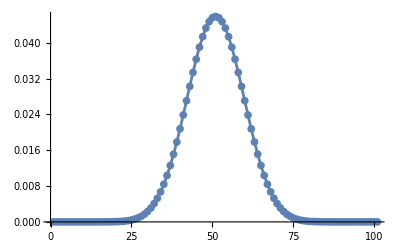

```mathematica
ListLinePlot[probsO1[[-1]],
PlotRange->All,
Mesh->All
]
```

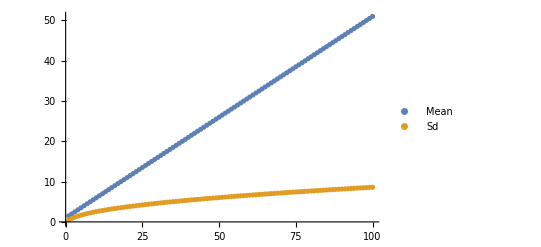

```mathematica
ListPlot[{expvalsO1,sdsO1},
PlotLegends->{"Mean","Sd"},
PlotRange->All
]
```

```mathematica
DTQWSdAdjustments[sdsO1]
```

FittedModel[0.854532 √x]